```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v5

```mathematica
dataall=Table[Import["./Shi_mu_960-1200_highT/Shi_mu="<>ToString[i]<>"_m0=700.0-51x120_VC=true.csv"],{i,960,1200,10}];
```

```mathematica
n=Length[Table[i,{i,960,1200,10}]]
```

25

```mathematica
pdata=Table[Table[Table[dataall[[n1]][[j*120+i]][[5]],{i,2,121}],{j,0,50}],{n1,1,25}];
```

```mathematica
Table[Table[Export["./mub"<>ToString[960+(i-1)*10]<>"/V"<>ToString[j]<>".dat",pdata[[i]][[j]]],{i,1,25}],{j,1,51}];
```

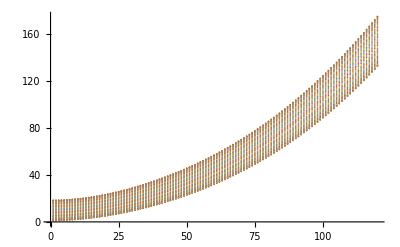

```mathematica
ListPlot[pdata[[1]]]
```